```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[8],Join[Table[{i,i-1},{i,Range[2,8,1]}],Table[{i,i+1},{i,Range[1,8,1]}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[8],Table[{2n,2n},{n,Range[1,4,1]}]->t]
```

```mathematica
T2[t_]:=T2[t]=ReplacePart[0*IdentityMatrix[8],Table[{2n-1,2n-1},{n,Range[1,4,1]}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.001,1,0]],A:=Inverse[β[ω,0.001,1,0]],B:=Inverse[β[ω,0.001,1,0]],T1:=T1[1],T2:=T2[1]},Do[J=Inverse[IdentityMatrix[8]-A.T1.Inverse[IdentityMatrix[8]-B.T2.J.T2].B.T1].A,3000];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[8]-g[ω,δ,t,ϵ].T2[t].LEFT[ω,δ,t,ϵ].T2[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SL[ω,δ,t,ϵ].T1[t].SR[ω,δ,t,ϵ].T1[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[8]-SR[ω,δ,t,ϵ].T1[t].SL[ω,δ,t,ϵ].T1[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].T1[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T1[t].grr[ω,δ,t,ϵ].T1[t]-T1[t].GNON[ω,δ,t,ϵ].T1[t].GNON[ω,δ,t,ϵ]]
```

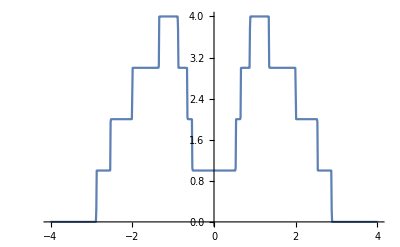
{195.498,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[-4,4,0.01]}]]]
```

```mathematica
υυ[ϵ1_,x_]:=Module[{μ1=RandomInteger[{1,8}], μ2=RandomInteger[{1,8}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,8}],μ5=RandomInteger[{1,8}], μ6=RandomInteger[{1,8}], μ7=RandomInteger[{1,8}],μ8=RandomInteger[{1,8}], μ9=RandomInteger[{6,11}]},Print[{μ1,μ2,μ3,μ5,μ6,μ8}];
η5:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[8]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[8]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[8]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[8]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[8]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[8]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[8]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[8]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[8]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[8]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];ρ93:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ94:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ95:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ96:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ97:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ98:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ99:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];listmax:={{2,ρ93},{3,ρ94},{4,ρ95},{5,ρ96},{6,ρ97},{7,ρ98},{8,ρ99}};ρρ93:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ94:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ95:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ96:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ97:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ98:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ99:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];listmin:={{2,ρρ93},{3,ρρ94},{4,ρρ95},{5,ρρ96},{6,ρρ97},{7,ρρ98},{8,ρρ99}};Print[listmin];Print[listmax];{{(*ListLinePlot[m5],*)listmax[[Position[listmax,Max[listmax]][[1,1]],1]],Max[listmax],ListLinePlot[listmax,PlotStyle->Red],listmin[[Position[listmin,Min[listmin]][[1,1]],1]],Min[listmin](*,
ListLinePlot[{{1,μ1},{2,μ2},{3,μ3},{4,μ4},{5,μ5},{6,μ6},{7,μ7},{8,μ8}},PlotStyle->RGBColor[RandomReal[{0.3,0.7}],RandomReal[{0.3,0.7}],RandomReal[{0.5,0.9}]]]*)}}]
```

{4,8,8,6,2,1}

{{2,0.00882319},{3,0.00704809},{4,0.00599129},{5,0.00558117},{6,0.00527934},{7,0.00544492},{8,0.00584789}}

{{2,666.327},{3,747.242},{4,903.287},{5,223.265},{6,121.999},{7,56.5866},{8,2616.72}}

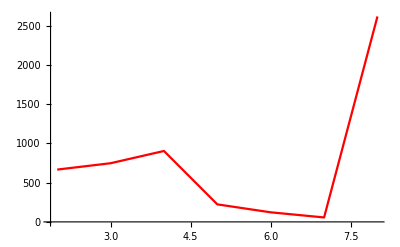
{{8,2616.72,-Graphics-,6,0.00527934}}

```mathematica
υυ[0.6,2.8]
```

```mathematica
ψψ[ϵ1_,x_]:=ψψ[ϵ1,x]=Table[υυ[ϵ1,x],500]
```

```mathematica
Clear[ψψ]
```

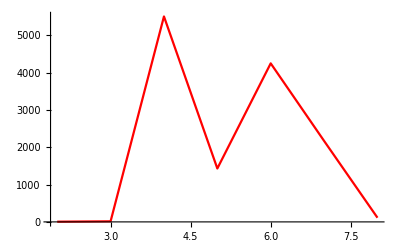
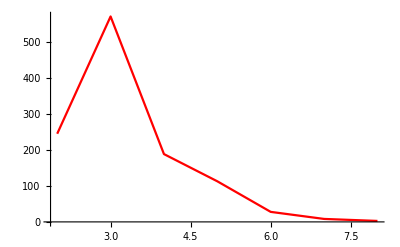
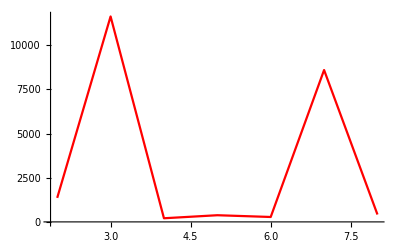
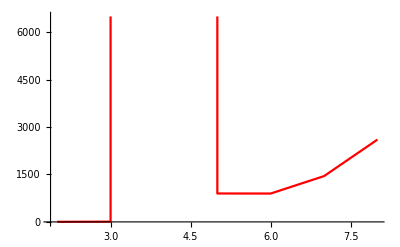
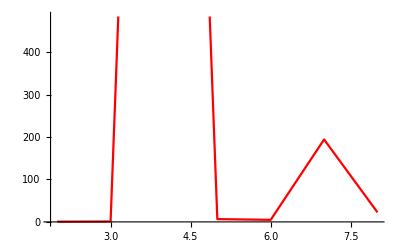
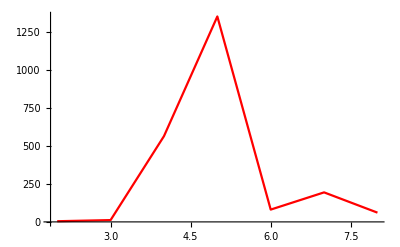
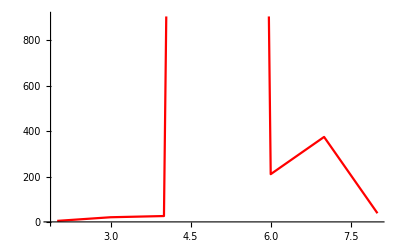
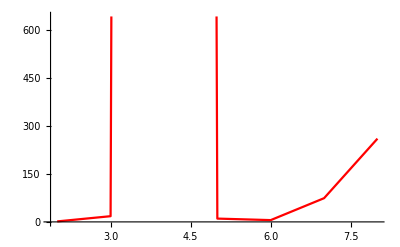
{{{4,5509.03,-Graphics-,6,0.00638902}},{{3,571.744,-Graphics-,5,0.0131898}},{{3,11631.3,-Graphics-,4,0.00968943}},{{4,1.07001×10^9,-Graphics-,7,0.00663913}},{{4,3346.8,-Graphics-,6,0.0105575}},{{5,1353.31,-Graphics-,5,0.00576975}},{{5,20412.8,-Graphics-,5,0.016977}},{{4,43270.2,-Graphics-,5,0.0032503}},{{7,2989.35,-Graphics-,4,0.00286609}},{{2,17846.1,-Graphics-,6,0.00455623}},{{6,549.079,-Graphics-,5,0.00540443}},{{6,213008.,-Graphics-,4,0.00248177}},{{4,1.24525×10^6,-Graphics-,5,0.0106708}},{{5,9359.47,-Graphics-,4,0.00271127}},{{5,91426.7,-Graphics-,4,0.00212401}},{{6,7775.73,-Graphics-,4,0.00210727}},{{2,72945.8,-Graphics-,5,0.023426}},{{5,936.461,-Graphics-,5,0.035389}},{{4,7886.89,-Graphics-,3,0.0027462}},{{2,2136.77,-Graphics-,6,0.00825946}},{{8,2608.98,-Graphics-,4,0.0021413}},{{5,30310.4,-Graphics-,8,0.0131369}},{{6,1.97077×10^6,-Graphics-,6,0.0192984}},{{4,23153.8,-Graphics-,4,0.013726}},{{3,17486.3,-Graphics-,8,0.00833695}},{{5,1096.5,-Graphics-,4,0.00318307}},{{7,621.689,-Graphics-,5,0.0064263}},{{3,42749.6,-Graphics-,6,0.0352718}},{{4,5615.63,-Graphics-,6,0.00494446}},{{4,2085.12,-Graphics-,6,0.00321682}},{{5,875037.,-Graphics-,5,0.0251593}},{{6,51962.3,-Graphics-,7,0.00469492}},{{6,13385.9,-Graphics-,5,0.0242675}},{{4,15713.9,-Graphics-,6,0.00323596}},{{6,338374.,-Graphics-,3,0.00176697}},{{4,24447.,-Graphics-,5,0.00178911}},{{2,5871.47,-Graphics-,6,0.00281291}},{{3,2.82777×10^6,-Graphics-,4,0.00163162}},{{7,24545.9,-Graphics-,5,0.0172981}},{{3,3771.7,-Graphics-,4,0.00788991}},{{5,21874.9,-Graphics-,3,0.00120004}},{{5,4552.46,-Graphics-,5,0.0193621}},{{8,11319.2,-Graphics-,5,0.00362207}},{{5,1502.8,-Graphics-,7,0.00212084}},{{8,4086.84,-Graphics-,6,0.0120458}},{{4,2707.4,-Graphics-,4,0.00237925}},{{6,13031.6,-Graphics-,8,0.00812326}},{{4,2.81575×10^7,-Graphics-,6,0.00259461}},{{7,1679.11,-Graphics-,6,0.00237599}},{{5,2299.51,-Graphics-,6,0.00253581}},{{4,41303.2,-Graphics-,6,0.00621596}},{{2,16304.8,-Graphics-,7,0.00626662}},{{6,17775.3,-Graphics-,5,0.00674386}},{{7,1947.34,-Graphics-,5,0.0165664}},{{3,703.661,-Graphics-,4,0.00199737}},{{5,50487.5,-Graphics-,5,0.00410963}},{{8,26689.7,-Graphics-,5,0.0424355}},{{7,1.36445×10^6,-Graphics-,6,0.00266014}},{{8,967.115,-Graphics-,6,0.00935546}},{{5,1287.58,-Graphics-,6,0.00615376}},{{4,6703.07,-Graphics-,5,0.0177125}},{{8,1219.24,-Graphics-,5,0.0158318}},{{4,77246.9,-Graphics-,4,0.00350957}},{{2,1041.74,-Graphics-,5,0.0257329}},{{2,12706.4,-Graphics-,4,0.00423438}},{{2,15282.9,-Graphics-,3,0.00222739}},{{3,27360.5,-Graphics-,7,0.00451041}},{{5,5622.46,-Graphics-,5,0.0789966}},{{2,6521.08,-Graphics-,4,0.00286353}},{{3,532.831,-Graphics-,4,0.0107981}},{{3,254.078,-Graphics-,3,0.00351896}},{{5,15653.9,-Graphics-,4,0.00351052}},{{6,1.69288×10^6,-Graphics-,4,0.00182082}},{{5,1523.37,-Graphics-,5,0.0150899}},{{2,2694.33,-Graphics-,4,0.00165222}},{{8,339116.,-Graphics-,4,0.00302555}},{{4,11211.2,-Graphics-,4,0.00254812}},{{3,8419.03,-Graphics-,4,0.00635346}},{{3,1.69578×10^6,-Graphics-,5,0.00678352}},{{6,755.98,-Graphics-,6,0.00508242}},{{3,5.42065×10^6,-Graphics-,4,0.00388439}},{{2,5625.2,-Graphics-,7,0.00376898}},{{2,563.068,-Graphics-,4,0.00189019}},{{7,7708.51,-Graphics-,4,0.00146235}},{{4,28982.3,-Graphics-,4,0.00226271}},{{6,526.579,-Graphics-,4,0.00115354}},{{3,14482.9,-Graphics-,6,0.00349864}},{{4,1614.67,-Graphics-,5,0.0021939}},{{8,58867.9,-Graphics-,6,0.00379771}},{{7,14553.5,-Graphics-,5,0.0230757}},{{8,9107.62,-Graphics-,4,0.00200524}},{{8,7527.92,-Graphics-,5,0.00217398}},{{3,2758.72,-Graphics-,3,0.00211371}},{{8,4225.14,-Graphics-,5,0.00209587}},{{3,13928.1,-Graphics-,4,0.00438883}},{{8,71123.6,-Graphics-,5,0.00893554}},{{6,73116.2,-Graphics-,6,0.00315097}},{{3,11896.6,-Graphics-,4,0.00209864}},{{2,2732.03,-Graphics-,7,0.00222645}},{{3,501.188,-Graphics-,8,0.0082469}},{{5,6497.57,-Graphics-,7,0.00490753}},{{7,55759.4,-Graphics-,5,0.0100686}},{{3,6419.93,-Graphics-,6,0.00294081}},{{7,84072.1,-Graphics-,7,0.00529671}},{{5,2003.77,-Graphics-,4,0.012264}},{{4,1347.72,-Graphics-,6,0.0189445}},{{5,909.702,-Graphics-,5,0.0117721}},{{2,4323.22,-Graphics-,4,0.00218342}},{{3,309116.,-Graphics-,5,0.00443206}},{{5,10234.4,-Graphics-,5,0.00668699}},{{2,8254.25,-Graphics-,5,0.00443063}},{{6,2489.93,-Graphics-,5,0.0322745}},{{4,7697.47,-Graphics-,4,0.00249197}},{{7,2.32689×10^7,-Graphics-,6,0.0101121}},{{3,33667.8,-Graphics-,3,0.00202595}},{{7,453.396,-Graphics-,3,0.00252818}},{{4,4253.95,-Graphics-,5,0.00169991}},{{2,2.81346×10^6,-Graphics-,5,0.00637745}},{{4,93619.,-Graphics-,6,0.00556162}},{{5,6755.09,-Graphics-,5,0.0108227}},{{6,29650.,-Graphics-,8,0.00609977}},{{6,9007.16,-Graphics-,6,0.00312373}},{{5,180655.,-Graphics-,5,0.00796621}},{{3,12286.5,-Graphics-,4,0.00274998}},{{7,38703.2,-Graphics-,6,0.00468261}},{{5,1756.8,-Graphics-,6,0.00358692}},{{7,1439.33,-Graphics-,5,0.00377074}},{{2,6739.01,-Graphics-,5,0.00614121}},{{6,21356.6,-Graphics-,4,0.00285485}},{{2,3240.87,-Graphics-,5,0.00301385}},{{2,52065.7,-Graphics-,7,0.00374061}},{{3,7552.49,-Graphics-,4,0.00321717}},{{6,29110.5,-Graphics-,4,0.00353523}},{{4,90857.9,-Graphics-,4,0.00435174}},{{3,1.68153×10^6,-Graphics-,6,0.00194028}},{{3,222817.,-Graphics-,3,0.00167904}},{{4,61377.6,-Graphics-,5,0.00548888}},{{4,3980.97,-Graphics-,5,0.00495732}},{{5,1032.79,-Graphics-,4,0.005296}},{{4,7074.76,-Graphics-,5,0.0192355}},{{2,12918.1,-Graphics-,6,0.00290323}},{{4,48862.4,-Graphics-,3,0.00173035}},{{8,55165.7,-Graphics-,5,0.0429145}},{{4,239205.,-Graphics-,5,0.0165772}},{{4,539120.,-Graphics-,6,0.00792024}},{{5,8576.05,-Graphics-,6,0.0134045}},{{2,11209.3,-Graphics-,6,0.00247032}},{{5,13521.9,-Graphics-,4,0.00179006}},{{3,8130.59,-Graphics-,5,0.0389889}},{{6,11455.9,-Graphics-,5,0.037932}},{{8,4410.1,-Graphics-,6,0.00427264}},{{4,36099.6,-Graphics-,5,0.00843039}},{{6,281835.,-Graphics-,5,0.0275173}},{{8,14059.1,-Graphics-,5,0.0276623}},{{2,41752.7,-Graphics-,4,0.00395805}},{{6,86257.7,-Graphics-,8,0.0120008}},{{5,551.349,-Graphics-,4,0.00413568}},{{3,8750.47,-Graphics-,4,0.00368709}},{{7,37508.1,-Graphics-,5,0.0144249}},{{7,1721.65,-Graphics-,4,0.00240488}},{{5,23.4172,-Graphics-,5,0.0189618}},{{4,6507.05,-Graphics-,6,0.00476529}},{{3,23691.7,-Graphics-,5,0.0192774}},{{5,468284.,-Graphics-,5,0.0136292}},{{5,306034.,-Graphics-,5,0.00216656}},{{6,7885.33,-Graphics-,5,0.0124552}},{{7,1239.43,-Graphics-,4,0.00354486}},{{5,15072.7,-Graphics-,6,0.00581761}},{{2,9134.37,-Graphics-,7,0.00345925}},{{2,448104.,-Graphics-,5,0.0342004}},{{3,7863.44,-Graphics-,4,0.00383798}},{{4,2414.55,-Graphics-,6,0.00216046}},{{6,9735.98,-Graphics-,6,0.00436839}},{{8,1304.58,-Graphics-,8,0.010861}},{{4,5684.98,-Graphics-,4,0.00281365}},{{3,3367.05,-Graphics-,4,0.00857834}},{{3,5743.7,-Graphics-,7,0.00573182}},{{4,1539.14,-Graphics-,5,0.0229986}},{{3,1988.33,-Graphics-,4,0.00246521}},{{6,274466.,-Graphics-,7,0.0131611}},{{7,43745.3,-Graphics-,4,0.00247458}},{{7,8437.6,-Graphics-,5,0.00195206}},{{2,7353.89,-Graphics-,5,0.0102863}},{{4,177683.,-Graphics-,5,0.00656181}},{{2,11183.4,-Graphics-,5,0.00731873}},{{5,6449.74,-Graphics-,6,0.0107396}},{{3,6720.61,-Graphics-,4,0.00244935}},{{6,1.09964×10^6,-Graphics-,5,0.0138216}},{{6,9.7479×10^7,-Graphics-,7,0.00292006}},{{3,6063.3,-Graphics-,4,0.00225311}},{{8,7716.02,-Graphics-,6,0.00643602}},{{5,3912.12,-Graphics-,5,0.00718162}},{{5,2016.81,-Graphics-,5,0.0260173}},{{4,37837.3,-Graphics-,4,0.00288572}},{{6,355758.,-Graphics-,4,0.00264107}},{{6,191318.,-Graphics-,4,0.00344537}},{{4,146487.,-Graphics-,5,0.00470144}},{{2,6340.25,-Graphics-,5,0.0162407}},{{5,245559.,-Graphics-,4,0.00289175}},{{8,1187.82,-Graphics-,4,0.00465416}},{{5,5753.06,-Graphics-,5,0.00515467}},{{2,10235.2,-Graphics-,6,0.00408058}},{{8,11440.2,-Graphics-,5,0.0120809}},{{4,1.51428×10^7,-Graphics-,4,0.0024965}},{{3,2209.27,-Graphics-,4,0.0015843}},{{4,319.332,-Graphics-,3,0.00825735}},{{7,5.29634×10^6,-Graphics-,5,0.0134873}},{{5,10637.1,-Graphics-,5,0.0253136}},{{6,3530.05,-Graphics-,5,0.007663}},{{8,1890.07,-Graphics-,7,0.00186001}},{{2,8029.66,-Graphics-,4,0.00140615}},{{6,21816.4,-Graphics-,5,0.00525116}},{{7,5382.38,-Graphics-,3,0.001149}},{{5,2472.63,-Graphics-,4,0.00301381}},{{7,1378.98,-Graphics-,4,0.00509806}},{{5,301040.,-Graphics-,4,0.00239891}},{{7,349167.,-Graphics-,5,0.0346905}},{{3,8039.77,-Graphics-,6,0.0103683}},{{2,13970.1,-Graphics-,4,0.00143956}},{{5,55866.9,-Graphics-,6,0.00419294}},{{7,5519.15,-Graphics-,4,0.00320041}},{{6,18764.2,-Graphics-,8,0.0132556}},{{4,5922.97,-Graphics-,5,0.0118655}},{{2,5306.41,-Graphics-,7,0.00250994}},{{4,7928.85,-Graphics-,5,0.00710191}},{{3,2685.08,-Graphics-,5,0.0185264}},{{7,808857.,-Graphics-,5,0.00285889}},{{6,1.93895×10^7,-Graphics-,6,0.0106648}},{{6,44413.9,-Graphics-,4,0.00211265}},{{7,460764.,-Graphics-,4,0.00232644}},{{5,17386.,-Graphics-,5,0.0141391}},{{4,23366.9,-Graphics-,5,0.0117846}},{{6,78052.9,-Graphics-,4,0.00323018}},{{8,4.75393×10^6,-Graphics-,5,0.00383975}},{{3,3660.24,-Graphics-,6,0.0029497}},{{8,14023.9,-Graphics-,4,0.00308676}},{{5,12842.3,-Graphics-,4,0.00426842}},{{5,5390.16,-Graphics-,6,0.0030592}},{{5,3.59973×10^6,-Graphics-,4,0.00164873}},{{2,20170.3,-Graphics-,4,0.00311927}},{{6,12975.5,-Graphics-,5,0.00663206}},{{4,8653.54,-Graphics-,5,0.00243742}},{{7,8758.16,-Graphics-,5,0.0153657}},{{3,26988.1,-Graphics-,4,0.00289352}},{{5,7901.24,-Graphics-,4,0.0023698}},{{3,67818.5,-Graphics-,4,0.00272757}},{{3,4090.46,-Graphics-,5,0.00293281}},{{3,9608.47,-Graphics-,3,0.00248382}},{{3,8667.28,-Graphics-,5,0.0330955}},{{8,4681.24,-Graphics-,8,0.0122601}},{{2,315559.,-Graphics-,5,0.0112821}},{{7,1935.87,-Graphics-,8,0.00549962}},{{4,28152.3,-Graphics-,4,0.00241857}},{{6,1887.22,-Graphics-,4,0.0103555}},{{3,87730.6,-Graphics-,6,0.00362473}},{{5,12276.3,-Graphics-,5,0.0169864}},{{6,1622.58,-Graphics-,3,0.00192068}},{{6,1679.46,-Graphics-,5,0.00877904}},{{7,113156.,-Graphics-,4,0.00367979}},{{6,27553.7,-Graphics-,5,0.00617973}},{{8,643.533,-Graphics-,5,0.00297937}},{{4,23627.2,-Graphics-,4,0.00241374}},{{4,12617.8,-Graphics-,5,0.0240813}},{{4,2.73161×10^6,-Graphics-,5,0.0195005}},{{5,1741.01,-Graphics-,3,0.00170152}},{{6,37129.,-Graphics-,4,0.00194408}},{{3,197736.,-Graphics-,4,0.00167923}},{{5,50538.,-Graphics-,5,0.191036}},{{8,1424.77,-Graphics-,4,0.00189325}},{{6,2249.23,-Graphics-,6,0.00246658}},{{4,5951.93,-Graphics-,5,0.00975924}},{{3,9279.01,-Graphics-,4,0.00276803}},{{5,1228.43,-Graphics-,4,0.00313585}},{{2,24159.9,-Graphics-,6,0.00798221}},{{3,10116.6,-Graphics-,6,0.00680781}},{{2,32796.8,-Graphics-,6,0.00341915}},{{5,17401.6,-Graphics-,5,0.0114251}},{{2,1390.72,-Graphics-,7,0.00163765}},{{3,2154.39,-Graphics-,4,0.00264606}},{{7,53657.3,-Graphics-,6,0.00463379}},{{4,1240.33,-Graphics-,5,0.00161336}},{{6,3408.64,-Graphics-,4,0.00262139}},{{7,1.89606×10^6,-Graphics-,6,0.00651898}},{{3,2031.88,-Graphics-,4,0.00413317}},{{2,63277.4,-Graphics-,5,0.0106858}},{{5,10629.8,-Graphics-,7,0.00414204}},{{4,5484.07,-Graphics-,3,0.00364439}},{{5,2299.51,-Graphics-,6,0.00253581}},{{2,902.362,-Graphics-,6,0.00424625}},{{4,5815.55,-Graphics-,8,0.0228051}},{{2,4254.68,-Graphics-,4,0.00255442}},{{5,61489.9,-Graphics-,4,0.00380346}},{{7,44404.2,-Graphics-,5,0.00347437}},{{7,45108.5,-Graphics-,5,0.0185631}},{{6,2663.49,-Graphics-,6,0.00560912}},{{4,5380.75,-Graphics-,4,0.00205548}},{{2,415100.,-Graphics-,4,0.00244086}},{{4,1090.18,-Graphics-,4,0.0034051}},{{5,57456.8,-Graphics-,4,0.00245262}},{{5,68401.2,-Graphics-,6,0.00825685}},{{5,120446.,-Graphics-,6,0.00268113}},{{3,1597.57,-Graphics-,4,0.00282381}},{{3,47614.2,-Graphics-,5,0.0400372}},{{4,8916.22,-Graphics-,4,0.00378678}},{{2,5240.56,-Graphics-,4,0.00297123}},{{4,859.236,-Graphics-,4,0.00209345}},{{2,62748.,-Graphics-,4,0.0028427}},{{2,24699.,-Graphics-,5,0.00333563}},{{8,705.616,-Graphics-,5,0.0280442}},{{4,29304.5,-Graphics-,6,0.00315268}},{{6,31845.5,-Graphics-,4,0.0028924}},{{7,11907.4,-Graphics-,5,0.0237647}},{{3,1946.59,-Graphics-,4,0.00379837}},{{3,532.831,-Graphics-,4,0.0107981}},{{6,1638.96,-Graphics-,4,0.00193004}},{{2,3476.19,-Graphics-,4,0.00464278}},{{8,314432.,-Graphics-,4,0.00368936}},{{7,2952.17,-Graphics-,4,0.00431695}},{{2,79478.5,-Graphics-,5,0.0456672}},{{2,6266.92,-Graphics-,6,0.00246713}},{{3,11914.,-Graphics-,4,0.00257505}},{{3,6599.57,-Graphics-,5,0.00607569}},{{2,9480.27,-Graphics-,4,0.00572827}},{{5,4014.13,-Graphics-,5,0.00981947}},{{7,5.89147×10^7,-Graphics-,8,0.00543495}},{{5,6141.73,-Graphics-,7,0.00575042}},{{5,4915.37,-Graphics-,6,0.00306015}},{{8,39.5877,-Graphics-,5,0.00478383}},{{3,33594.1,-Graphics-,4,0.00281386}},{{7,592.416,-Graphics-,5,0.0171291}},{{5,1.48302×10^7,-Graphics-,7,0.0102537}},{{7,2.11926×10^7,-Graphics-,4,0.00242311}},{{5,2434.79,-Graphics-,5,0.0428427}},{{2,33013.9,-Graphics-,8,0.00487631}},{{3,187615.,-Graphics-,4,0.00277855}},{{2,1.0697×10^6,-Graphics-,3,0.000822776}},{{7,6371.56,-Graphics-,3,0.00340914}},{{8,13283.7,-Graphics-,5,0.0185975}},{{4,4196.09,-Graphics-,6,0.0248787}},{{3,2998.55,-Graphics-,4,0.00332834}},{{7,5002.07,-Graphics-,5,0.00562391}},{{3,48794.9,-Graphics-,4,0.002373}},{{4,30162.4,-Graphics-,6,0.00556009}},{{8,269.708,-Graphics-,5,0.00697485}},{{8,9000.6,-Graphics-,5,0.0303776}},{{5,31223.2,-Graphics-,4,0.00324682}},{{5,2.82458×10^6,-Graphics-,4,0.00320865}},{{2,7411.98,-Graphics-,6,0.00950108}},{{3,15472.1,-Graphics-,7,0.00577981}},{{7,23761.6,-Graphics-,5,0.00598711}},{{5,11395.2,-Graphics-,6,0.00232056}},{{4,2087.63,-Graphics-,5,0.0228722}},{{2,704347.,-Graphics-,5,0.00738599}},{{6,2.88747×10^6,-Graphics-,4,0.00310282}},{{5,478924.,-Graphics-,4,0.00346023}},{{3,3132.06,-Graphics-,5,0.0120523}},{{3,2032.68,-Graphics-,4,0.00219108}},{{7,5534.1,-Graphics-,5,0.00846291}},{{6,9634.03,-Graphics-,5,0.0127991}},{{4,34744.3,-Graphics-,5,0.00175141}},{{6,3131.03,-Graphics-,5,0.00465863}},{{4,10153.,-Graphics-,4,0.00264955}},{{3,83726.3,-Graphics-,4,0.00302171}},{{2,17910.6,-Graphics-,6,0.00452664}},{{3,71595.7,-Graphics-,5,0.0145534}},{{7,40105.5,-Graphics-,5,0.00522424}},{{6,63571.9,-Graphics-,7,0.00438951}},{{3,23616.4,-Graphics-,7,0.00226481}},{{2,41728.4,-Graphics-,4,0.00282479}},{{4,2218.04,-Graphics-,5,0.0194911}},{{7,4270.55,-Graphics-,5,0.00637957}},{{2,5734.05,-Graphics-,8,0.00374296}},{{2,25538.8,-Graphics-,5,0.00238164}},{{4,4457.34,-Graphics-,5,0.0100723}},{{4,28212.6,-Graphics-,5,0.003185}},{{2,443.637,-Graphics-,4,0.00228995}},{{6,21742.8,-Graphics-,6,0.00337621}},{{2,1367.99,-Graphics-,6,0.00294023}},{{2,109901.,-Graphics-,6,0.0149946}},{{8,4020.36,-Graphics-,4,0.00711556}},{{8,1303.27,-Graphics-,6,0.0125669}},{{4,1696.9,-Graphics-,4,0.00256992}},{{6,2722.64,-Graphics-,8,0.0442401}},{{5,1928.78,-Graphics-,4,0.00670155}},{{6,201712.,-Graphics-,6,0.00417181}},{{3,12497.2,-Graphics-,8,0.0055136}},{{4,12772.6,-Graphics-,4,0.00217832}},{{8,444141.,-Graphics-,4,0.00209454}},{{3,33143.5,-Graphics-,3,0.00155503}},{{5,1.62162×10^7,-Graphics-,4,0.00166841}},{{4,5110.4,-Graphics-,6,0.00279912}},{{4,476.953,-Graphics-,7,0.00429662}},{{6,9664.87,-Graphics-,4,0.00182959}},{{4,78143.9,-Graphics-,7,0.00447317}},{{8,10244.7,-Graphics-,6,0.00216086}},{{6,67740.6,-Graphics-,6,0.00236612}},{{2,7009.93,-Graphics-,6,0.00361136}},{{3,43074.9,-Graphics-,7,0.00329474}},{{8,57898.1,-Graphics-,7,0.00422542}},{{6,6.34018×10^6,-Graphics-,6,0.00456729}},{{8,733.888,-Graphics-,5,0.0156275}},{{3,143405.,-Graphics-,7,0.00497442}},{{2,2.35857×10^6,-Graphics-,4,0.00218593}},{{2,13322.9,-Graphics-,4,0.002219}},{{5,7315.65,-Graphics-,5,0.00299594}},{{8,23442.9,-Graphics-,6,0.00299136}},{{8,18992.1,-Graphics-,4,0.00309188}},{{6,22353.3,-Graphics-,5,0.00465358}},{{3,8970.01,-Graphics-,6,0.00394351}},{{2,9858.68,-Graphics-,4,0.00399216}},{{7,2210.56,-Graphics-,5,0.0166326}},{{7,3.64671×10^7,-Graphics-,5,0.0016225}},{{2,28758.1,-Graphics-,4,0.00148437}},{{7,15546.2,-Graphics-,5,0.0213324}},{{2,80401.2,-Graphics-,6,0.00146925}},{{3,87257.1,-Graphics-,4,0.0020113}},{{4,13367.8,-Graphics-,5,0.0108466}},{{6,33491.5,-Graphics-,7,0.00399174}},{{2,2735.45,-Graphics-,6,0.00774791}},{{3,7705.44,-Graphics-,4,0.002441}},{{8,1973.5,-Graphics-,5,0.0228356}},{{5,2119.02,-Graphics-,4,0.00393792}},{{5,66069.7,-Graphics-,7,0.00196187}},{{4,1000.59,-Graphics-,5,0.0138071}},{{5,3419.19,-Graphics-,5,0.00769442}},{{5,1.16169×10^7,-Graphics-,3,0.00203936}},{{3,20819.8,-Graphics-,4,0.00553245}},{{2,1.05583×10^6,-Graphics-,6,0.0182502}},{{4,2063.29,-Graphics-,4,0.00319022}},{{8,1695.98,-Graphics-,8,0.013845}},{{2,17858.3,-Graphics-,5,0.00867621}},{{4,1.80346×10^6,-Graphics-,3,0.0035413}},{{8,8,-Graphics-,4,0.00296522}},{{8,1459.74,-Graphics-,5,0.00293801}},{{5,2200.67,-Graphics-,6,0.00357258}},{{7,84965.1,-Graphics-,6,0.00231488}},{{6,1.29393×10^6,-Graphics-,4,0.00461761}},{{7,25347.,-Graphics-,4,0.00303224}},{{2,3537.41,-Graphics-,4,0.0014515}},{{5,140709.,-Graphics-,3,0.00222418}},{{7,4674.32,-Graphics-,4,0.00479977}},{{8,660717.,-Graphics-,6,0.00341539}},{{4,6.05135×10^7,-Graphics-,4,0.00363407}},{{2,3659.99,-Graphics-,7,0.00368037}},{{2,6784.59,-Graphics-,4,0.00328191}},{{2,43236.8,-Graphics-,4,0.00253346}},{{5,2953.18,-Graphics-,6,0.00470246}},{{2,601131.,-Graphics-,4,0.00303662}},{{3,25491.8,-Graphics-,4,0.00201067}},{{2,94907.5,-Graphics-,6,0.00154735}},{{2,1.65056×10^6,-Graphics-,4,0.00130173}},{{5,1938.2,-Graphics-,5,0.00880748}},{{7,3417.88,-Graphics-,4,0.00224235}},{{2,24570.2,-Graphics-,4,0.00268165}},{{5,1433.86,-Graphics-,7,0.0029417}},{{2,637.3,-Graphics-,5,0.0106369}},{{4,7666.25,-Graphics-,6,0.00317969}},{{7,1578.75,-Graphics-,5,0.00146627}},{{2,5601.52,-Graphics-,5,0.00497425}},{{4,1480.62,-Graphics-,3,0.00119694}},{{2,697.316,-Graphics-,6,0.00353655}},{{5,6121.49,-Graphics-,8,0.0313137}},{{3,365597.,-Graphics-,3,0.00616934}},{{8,2942.05,-Graphics-,6,0.00327185}},{{4,16156.4,-Graphics-,4,0.00183546}},{{3,42271.5,-Graphics-,6,0.00349015}},{{4,42081.1,-Graphics-,5,0.03688}},{{4,1.08215×10^6,-Graphics-,6,0.00249675}},{{4,22060.7,-Graphics-,8,0.0069728}},{{4,2546.22,-Graphics-,4,0.00710462}},{{2,187208.,-Graphics-,6,0.00315105}},{{6,2.04501×10^6,-Graphics-,5,0.00840074}},{{5,1.64255×10^6,-Graphics-,7,0.0390291}},{{3,785.408,-Graphics-,6,0.00148917}},{{3,4395.64,-Graphics-,5,0.00483818}},{{4,8237.31,-Graphics-,5,0.00941219}},{{5,37820.2,-Graphics-,4,0.00325591}},{{7,1370.45,-Graphics-,6,0.023903}},{{6,6443.27,-Graphics-,5,0.00523955}},{{8,401999.,-Graphics-,5,0.0107157}},{{7,4843.36,-Graphics-,8,0.00990873}},{{3,11910.8,-Graphics-,7,0.00298439}},{{3,134978.,-Graphics-,4,0.00435368}},{{7,390.843,-Graphics-,8,0.0148029}},{{6,9275.45,-Graphics-,4,0.00234045}},{{8,477.365,-Graphics-,4,0.00621938}},{{4,1793.91,-Graphics-,6,0.0114698}},{{8,3752.82,-Graphics-,4,0.00124186}},{{8,750.124,-Graphics-,4,0.00224683}},{{6,2152.38,-Graphics-,4,0.00337876}},{{4,1297.29,-Graphics-,4,0.00173229}},{{3,19629.6,-Graphics-,4,0.00273157}},{{8,1044.64,-Graphics-,5,0.00249234}},{{2,8805.22,-Graphics-,5,0.0051614}},{{7,10995.,-Graphics-,4,0.00978276}},{{4,4572.58,-Graphics-,5,0.00116557}},{{7,8413.56,-Graphics-,5,0.0501362}},{{7,1222.27,-Graphics-,5,0.00278831}},{{2,15212.,-Graphics-,4,0.00252003}},{{4,37590.9,-Graphics-,6,0.00249286}}}

```mathematica
ψψ[0.6,2]
```

```mathematica
Table[ψψ[0.6,2][[x]][[1,4]],{x,500}]
```

```mathematica
{6,5,4,7,6,5,5,5,4,6,5,4,5,4,4,4,5,5,3,6,4,8,6,4,8,4,5,6,6,6,5,7,5,6,3,5,6,4,5,4,3,5,5,7,6,4,8,6,6,6,6,7,5,5,4,5,5,6,6,6,5,5,4,5,4,3,7,5,4,4,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,5,6,4,7,4,4,4,4,6,5,6,5,4,5,3,5,4,5,6,4,7,8,7,5,6,7,4,6,5,4,5,5,5,5,4,6,3,3,5,5,6,5,8,6,5,4,6,6,5,5,4,5,7,4,4,4,6,3,5,5,4,5,6,3,5,5,6,6,6,4,5,5,6,5,5,5,4,8,4,4,5,4,5,6,5,5,5,5,4,6,7,5,4,6,6,8,4,4,7,5,4,7,4,5,5,5,5,6,4,5,7,4,6,5,5,4,4,4,5,5,4,4,5,6,5,4,4,3,5,5,5,7,4,5,3,4,4,4,5,6,4,6,4,8,5,7,5,5,5,6,4,4,5,5,4,5,6,4,4,6,4,4,5,5,5,4,4,4,5,3,5,8,5,8,4,4,6,5,3,5,4,5,5,4,5,5,3,4,4,5,4,6,5,4,4,6,6,6,5,7,4,6,5,4,6,4,5,7,3,6,6,8,4,4,5,5,6,4,4,4,4,6,6,4,5,4,4,4,4,5,5,6,4,5,4,4,4,4,4,4,5,6,4,5,4,5,8,7,6,5,4,5,7,4,5,8,4,3,3,5,6,4,5,4,6,5,5,4,4,6,7,5,6,5,5,4,4,5,4,5,5,5,5,4,4,6,5,5,7,7,4,5,5,8,5,5,5,4,6,6,6,4,6,4,8,4,6,8,4,4,3,4,6,7,4,7,6,6,6,7,7,6,5,7,4,4,5,6,4,5,6,4,5,5,4,5,6,4,5,7,6,4,5,4,7,5,5,3,4,6,4,8,5,3,4,5,6,6,4,4,4,3,4,6,4,7,4,4,6,4,4,6,4,5,4,4,7,5,6,5,5,3,6,8,3,6,4,6,5,6,8,4,6,5,7,6,5,5,4,6,5,5,8,7,4,8,4,4,6,4,4,4,4,4,5,5,4,5,5,5,4,6}
```

{6,5,4,7,6,5,5,5,4,6,5,4,5,4,4,4,5,5,3,6,4,8,6,4,8,4,5,6,6,6,5,7,5,6,3,5,6,4,5,4,3,5,5,7,6,4,8,6,6,6,6,7,5,5,4,5,5,6,6,6,5,5,4,5,4,3,7,5,4,4,3,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,5,6,4,7,4,4,4,4,6,5,6,5,4,5,3,5,4,5,6,4,7,8,7,5,6,7,4,6,5,4,5,5,5,5,4,6,3,3,5,5,6,5,8,6,5,4,6,6,5,5,4,5,7,4,4,4,6,3,5,5,4,5,6,3,5,5,6,6,6,4,5,5,6,5,5,5,4,8,4,4,5,4,5,6,5,5,5,5,4,6,7,5,4,6,6,8,4,4,7,5,4,7,4,5,5,5,5,6,4,5,7,4,6,5,5,4,4,4,5,5,4,4,5,6,5,4,4,3,5,5,5,7,4,5,3,4,4,4,5,6,4,6,4,8,5,7,5,5,5,6,4,4,5,5,4,5,6,4,4,6,4,4,5,5,5,4,4,4,5,3,5,8,5,8,4,4,6,5,3,5,4,5,5,4,5,5,3,4,4,5,4,6,5,4,4,6,6,6,5,7,4,6,5,4,6,4,5,7,3,6,6,8,4,4,5,5,6,4,4,4,4,6,6,4,5,4,4,4,4,5,5,6,4,5,4,4,4,4,4,4,5,6,4,5,4,5,8,7,6,5,4,5,7,4,5,8,4,3,3,5,6,4,5,4,6,5,5,4,4,6,7,5,6,5,5,4,4,5,4,5,5,5,5,4,4,6,5,5,7,7,4,5,5,8,5,5,5,4,6,6,6,4,6,4,8,4,6,8,4,4,3,4,6,7,4,7,6,6,6,7,7,6,5,7,4,4,5,6,4,5,6,4,5,5,4,5,6,4,5,7,6,4,5,4,7,5,5,3,4,6,4,8,5,3,4,5,6,6,4,4,4,3,4,6,4,7,4,4,6,4,4,6,4,5,4,4,7,5,6,5,5,3,6,8,3,6,4,6,5,6,8,4,6,5,7,6,5,5,4,6,5,5,8,7,4,8,4,4,6,4,4,4,4,4,5,5,4,5,5,5,4,6}

```mathematica
Length[%61]
```

538

```mathematica
Count[%61,5]+Count[%61,4]+Count[%61,6]
```

```mathematica
459/538
```

459/538

```mathematica
N[459/538]
```

0.85316

```mathematica
Histogram[%61,ChartStyle->{Opacity[0.5],{Red, Green,Green,Green,Red,Red}}]
```

-Graphics-

```mathematica
Histogram[%61,PlotTheme->"Scientific",ChartStyle->{Opacity[0.5],{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,1,0],RGBColor[0,1,0],RGBColor[1,0,0],RGBColor[1,0,0]}}]
```

-Graphics-

```mathematica
Show[%63,FrameLabel->{{None,None},{HoldForm[Number of impurities],None}},PlotLabel->HoldForm[χ],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Histogram[%52,ChartStyle->{Opacity[0.5],{Red,Red ,Green,Green,Green,Red,Red}}]
```

-Graphics-

```mathematica
Histogram[%52,PlotTheme->"Detailed",ChartStyle->{Opacity[0.5],{RGBColor[1,0,0],RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,1,0],RGBColor[0,1,0],RGBColor[1,0,0],RGBColor[1,0,0]}}]
```

-Graphics-

```mathematica
Show[%65,FrameLabel->{{None,None},{HoldForm[Number of impurities],None}},PlotLabel->HoldForm[η],LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Table[ψψ[0.6,2][[x]][[1,1]],{x,500}]
```

{4,3,3,4,4,5,5,4,7,2,6,6,4,5,5,6,2,5,4,2,8,5,6,4,3,5,7,3,4,4,5,6,6,4,6,4,2,3,7,3,5,5,8,5,8,4,6,4,7,5,4,2,6,7,3,5,8,7,8,5,4,8,4,2,2,2,3,5,2,3,3,5,6,5,2,8,4,3,3,6,3,2,2,7,4,6,3,4,8,7,8,8,3,8,3,8,6,3,2,3,5,7,3,7,5,4,5,2,3,5,2,6,4,7,3,7,4,2,4,5,6,6,5,3,7,5,7,2,6,2,2,3,6,4,3,3,4,4,5,4,2,4,8,4,4,5,2,5,3,6,8,4,6,8,2,6,5,3,7,7,5,4,3,5,5,6,7,5,2,2,3,4,6,8,4,3,3,4,3,6,7,7,2,4,2,5,3,6,6,3,8,5,5,4,6,6,4,2,5,8,5,2,8,4,3,4,7,5,6,8,2,6,7,5,7,5,7,3,2,5,7,6,4,2,4,3,7,6,6,7,5,4,6,8,3,8,5,5,5,2,6,4,7,3,5,3,3,3,3,8,2,7,4,6,3,5,6,6,7,6,8,4,4,4,5,6,3,5,8,6,4,3,5,2,3,2,5,2,3,7,4,6,7,3,2,5,4,5,2,4,2,5,7,7,6,4,2,4,5,5,5,3,3,4,2,4,2,2,8,4,6,7,3,3,6,2,8,7,2,2,3,3,2,5,7,5,5,8,3,7,5,7,5,2,3,2,7,8,4,3,7,3,4,8,8,5,5,2,3,7,5,4,2,6,5,3,3,7,6,4,6,4,3,2,3,7,6,3,2,4,7,2,2,4,4,2,6,2,2,8,8,4,6,5,6,3,4,8,3,5,4,4,6,4,8,6,2,3,8,6,8,3,2,2,5,8,8,6,3,2,7,7,2,7,2,3,4,6,2,3,8,5,5,4,5,5,3,2,4,8,2,4,8,8,5,7,6,7,2,5,7,8,4,2,2,2,5,2,3,2,2,5,7,2,5,2,4,7,2,4,2,5,3,8,4,3,4,4,4,4,2,6,5,3,3,4,5,7,6,8,7,3,3,7,6,8,4,8,8,6,4,3,8,2,7,4,7,7,2,4}

```mathematica
Histogram[%52,ChartStyle->{Red,Green,Green,Green,Red,Red}]
```

-Graphics-

```mathematica
ρ[ϵ1_,x_]:=Module[{μ1=RandomInteger[{1,8}], μ2=RandomInteger[{1,8}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,8}],μ5=RandomInteger[{1,8}], μ6=RandomInteger[{1,8}], μ7=RandomInteger[{1,8}],μ8=RandomInteger[{1,8}], μ9=RandomInteger[{6,11}]},Print[{μ1(*,μ2*),μ3,μ5,μ7,μ8}];
η5:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-ϵ1]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-ϵ1]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[8]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[8]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[8]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[8]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[8]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[8]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[8]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[8]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[8]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[8]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]];Clear[m5];m5:=m5=Table[{ω,η5},{ω,Range[0,4,0.01]}];
Show[ListLinePlot[m5,PlotStyle->Red],%89](*ρ93:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ94:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ95:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ96:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ97:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ98:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρ99:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],1/(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];listmax:={{2,ρ93},{3,ρ94},{4,ρ95},{5,ρ96},{6,ρ97},{7,ρ98},{8,ρ99}};ρρ93:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR/2imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ94:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//3imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ95:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//4imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ96:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//5imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ97:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//6imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ98:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//7imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];ρρ99:=Module[{B1=Transpose[{m5[[1;;400]][[;;,1]],(m5[[1;;400,2]]- Import["/home/shardulmukim/PhD/fwi/8AGNR//8imp6.csv"][[1;;400,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,0,x}]/(x*100)];listmin:={{2,ρρ93},{3,ρρ94},{4,ρρ95},{5,ρρ96},{6,ρρ97},{7,ρρ98},{8,ρρ99}};Print[listmin];Print[listmax];{{(*ListLinePlot[m5],*)listmax[[Position[listmax,Max[listmax]][[1,1]],1]],Max[listmax],ListLinePlot[listmax,PlotStyle->Red],listmin[[Position[listmin,Min[listmin]][[1,1]],1]],Min[listmin](*,
ListLinePlot[{{1,μ1},{2,μ2},{3,μ3},{4,μ4},{5,μ5},{6,μ6},{7,μ7},{8,μ8}},PlotStyle->RGBColor[RandomReal[{0.3,0.7}],RandomReal[{0.3,0.7}],RandomReal[{0.5,0.9}]]]*)}}*)]
```

```mathematica
ρ[0.5,0]
```

{8,6,4,3,6}

-Graphics-

```mathematica
ρ[00,0]
```

{5,2,2,1,4}

-Graphics-

-Graphics-

```mathematica
ene3[ω_,ϵ1_,x_]:=Module[{μ1=RandomInteger[{1,8}], μ2=RandomInteger[{1,8}], μ3=RandomInteger[{1,8}], μ4=RandomInteger[{1,8}],μ5=RandomInteger[{1,8}], μ6=RandomInteger[{1,8}], μ7=RandomInteger[{1,8}],μ8=RandomInteger[{1,8}], μ9=RandomInteger[{6,11}]},Print[{μ1,μ2,μ3,μ5,μ6,μ8}];
η5:=Module[{g:=Inverse[β[ω,0.001,1,0]]},
imp1=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*0.001-ϵ1]]];imp2=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ2,μ2}}->ω+ⅈ*0.001-0]]];imp3=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ3,μ3}}->ω+ⅈ*0.001-0]]];imp4=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ4,μ4}}->ω+ⅈ*0.001-0]]];imp5=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ5,μ5}}->ω+ⅈ*0.001-ϵ1]]];imp6=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ6,μ6}}->ω+ⅈ*0.001-0]]];imp7=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ7,μ7}}->ω+ⅈ*0.001-0]]];imp8=Inverse[Module[{gg=β[ω,0.001,1,0]},ReplacePart[gg,{{μ8,μ8}}->ω+ⅈ*0.001-ϵ1]]];Sl11:=Inverse[IdentityMatrix[8]-imp1.T1[1].SL[ω,0.001,1,0].T1[1]].imp1;Sl12:=Inverse[IdentityMatrix[8]-imp2.T2[1].Sl11.T2[1]].imp2;Sl13:=Inverse[IdentityMatrix[8]-imp3.T1[1].Sl12.T1[1]].imp3;Sl14:=Inverse[IdentityMatrix[8]-imp4.T2[1].Sl13.T2[1]].imp4;Sl15:=Inverse[IdentityMatrix[8]-imp5.T1[1].Sl14.T1[1]].imp5;Sl16:=Inverse[IdentityMatrix[8]-imp6.T2[1].Sl15.T2[1]].imp6;Sl17:=Inverse[IdentityMatrix[8]-imp7.T1[1].Sl16.T1[1]].imp7;Sl18:=Inverse[IdentityMatrix[8]-imp8.T2[1].Sl17.T2[1]].imp8;Il1:=Inverse[IdentityMatrix[8]-Sl18.T1[1].SR[ω,0.001,1,0].T1[1]].Sl18;Ir1:=Inverse[IdentityMatrix[8]-SR[ω,0.001,1,0].T1[1].Sl18.T1[1]].SR[ω,0.001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.001,1,0].T1[1].Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];{gdd1,grr1,GNON1}];η5]
```

```mathematica
ene3[1,1,0]
```

{6,7,3,2,6,7}

{{{0.-1.42642 ⅈ,1.40348×10^-11-0.187888 ⅈ,2.72427×10^-11+0.854372 ⅈ,6.08902×10^-12-0.144063 ⅈ,-1.44275×10^-11-0.337583 ⅈ,-1.39377×10^-11+0.336027 ⅈ,-6.97623×10^-12+0.080835 ⅈ,-1.4548×10^-11-0.384578 ⅈ},{-1.40348×10^-11-0.187888 ⅈ,0.-1.63757 ⅈ,-4.67759×10^-12-1.15662 ⅈ,-1.08227×10^-11-0.168792 ⅈ,2.56137×10^-11-0.065278 ⅈ,-6.1581×10^-12-0.323228 ⅈ,-6.26822×10^-11-0.0829996 ⅈ,2.0556×10^-11+0.309597 ⅈ},{-2.72427×10^-11+0.854372 ⅈ,4.67759×10^-12-1.15662 ⅈ,0.-2.45931 ⅈ,2.57018×10^-11-0.948188 ⅈ,6.58526×10^-11+0.222388 ⅈ,7.14984×10^-12-0.248826 ⅈ,-5.5411×10^-11-0.261781 ⅈ,-3.31823×10^-12+0.275876 ⅈ},{-6.08902×10^-12-0.144063 ⅈ,1.08227×10^-11-0.168792 ⅈ,-2.57018×10^-11-0.948188 ⅈ,0.-1.49846 ⅈ,4.38218×10^-11-0.6655 ⅈ,3.07675×10^-12+0.262835 ⅈ,-1.84358×10^-11-0.0928053 ⅈ,-3.39699×10^-12-0.486682 ⅈ},{1.44275×10^-11-0.337583 ⅈ,-2.56137×10^-11-0.065278 ⅈ,-6.58526×10^-11+0.222388 ⅈ,-4.38218×10^-11-0.6655 ⅈ,0.-1.36599 ⅈ,4.60798×10^-12-0.248927 ⅈ,-1.64835×10^-12+0.0267175 ⅈ,2.75363×10^-11-0.39331 ⅈ},{1.39377×10^-11+0.336027 ⅈ,6.1581×10^-12-0.323228 ⅈ,-7.14984×10^-12-0.248826 ⅈ,-3.07675×10^-12+0.262835 ⅈ,-4.60798×10^-12-0.248927 ⅈ,0.-1.28292 ⅈ,1.38428×10^-11-0.463699 ⅈ,1.38033×10^-11+0.801985 ⅈ},{6.97623×10^-12+0.080835 ⅈ,6.26822×10^-11-0.0829996 ⅈ,5.5411×10^-11-0.261781 ⅈ,1.84358×10^-11-0.0928053 ⅈ,1.64835×10^-12+0.0267175 ⅈ,-1.38428×10^-11-0.463699 ⅈ,0.-0.897311 ⅈ,8.64253×10^-12+0.0199732 ⅈ},{1.4548×10^-11-0.384578 ⅈ,-2.0556×10^-11+0.309597 ⅈ,3.31823×10^-12+0.275876 ⅈ,3.39699×10^-12-0.486682 ⅈ,-2.75363×10^-11-0.39331 ⅈ,-1.38033×10^-11+0.801985 ⅈ,-8.64253×10^-12+0.0199732 ⅈ,0.-1.68949 ⅈ}},{{0.-1.42931 ⅈ,1.33921×10^-11-0.385187 ⅈ,2.71482×10^-11+0.853475 ⅈ,6.52911×10^-12+0.657576 ⅈ,-1.45469×10^-11-0.339435 ⅈ,-7.55862×10^-12-0.590656 ⅈ,-6.84278×10^-12+0.0820986 ⅈ,8.11329×10^-12+0.463256 ⅈ},{-1.33921×10^-11-0.385187 ⅈ,0.-1.12598 ⅈ,3.21237×10^-11-0.44838 ⅈ,1.51613×10^-11+0.424469 ⅈ,2.55682×10^-11-0.0502504 ⅈ,2.66661×10^-11-0.557888 ⅈ,4.5295×10^-13-0.0977205 ⅈ,3.88503×10^-11+0.320209 ⅈ},{-2.71482×10^-11+0.853475 ⅈ,-3.21237×10^-11-0.44838 ⅈ,0.-2.45593 ⅈ,4.03793×10^-11-1.28585 ⅈ,6.5917×10^-11+0.222474 ⅈ,3.25978×10^-12+0.207206 ⅈ,-5.55371×10^-11-0.262303 ⅈ,-5.23734×10^-11-0.535273 ⅈ},{-6.52911×10^-12+0.657576 ⅈ,-1.51613×10^-11+0.424469 ⅈ,-4.03793×10^-11-1.28585 ⅈ,0.-1.65113 ⅈ,2.22889×10^-11-0.479581 ⅈ,-2.52336×10^-11+0.140037 ⅈ,-3.87913×10^-11-0.141459 ⅈ,-6.63934×10^-11-0.511022 ⅈ},{1.45469×10^-11-0.339435 ⅈ,-2.55682×10^-11-0.0502504 ⅈ,-6.5917×10^-11+0.222474 ⅈ,-2.22889×10^-11-0.479581 ⅈ,0.-1.36769 ⅈ,-6.1281×10^-12-1.0888 ⅈ,-1.49757×10^-12+0.0278702 ⅈ,-2.90719×10^-11+0.418443 ⅈ},{7.55862×10^-12-0.590656 ⅈ,-2.66661×10^-11-0.557888 ⅈ,-3.25978×10^-12+0.207206 ⅈ,2.52336×10^-11+0.140037 ⅈ,6.1281×10^-12-1.0888 ⅈ,0.-2.0662 ⅈ,-1.53774×10^-11-0.407443 ⅈ,-3.78215×10^-11+0.767935 ⅈ},{6.84278×10^-12+0.0820986 ⅈ,-4.5295×10^-13-0.0977205 ⅈ,5.55371×10^-11-0.262303 ⅈ,3.87913×10^-11-0.141459 ⅈ,1.49757×10^-12+0.0278702 ⅈ,1.53774×10^-11-0.407443 ⅈ,0.-0.898577 ⅈ,-8.60756×10^-12-0.916249 ⅈ},{-8.11329×10^-12+0.463256 ⅈ,-3.88503×10^-11+0.320209 ⅈ,5.23734×10^-11-0.535273 ⅈ,6.63934×10^-11-0.511022 ⅈ,2.90719×10^-11+0.418443 ⅈ,3.78215×10^-11+0.767935 ⅈ,8.60756×10^-12-0.916249 ⅈ,0.-2.62508 ⅈ}},{{0.+1.41989 ⅈ,-0.308257+0.28651 ⅈ,-0.000132176-0.847941 ⅈ,0.0546949-0.257467 ⅈ,-0.0000241012+0.334523 ⅈ,-0.125271+0.128659 ⅈ,0.0000893685-0.0794743 ⅈ,0.235843-0.0410867 ⅈ},{0.308257+0.28651 ⅈ,0.-0.292529 ⅈ,0.0183213+0.801518 ⅈ,0.285918+0.988059 ⅈ,0.0877554+0.0583269 ⅈ,-0.193647-0.292286 ⅈ,-0.0252898+0.0901473 ⅈ,0.160023+0.405123 ⅈ},{0.000132176-0.847941 ⅈ,-0.0183213+0.801518 ⅈ,0.+2.45164 ⅈ,0.411195+1.11731 ⅈ,0.000285637-0.218443 ⅈ,-0.324253+0.0198157 ⅈ,-0.000115232+0.260049 ⅈ,0.109467+0.131234 ⅈ},{-0.0546949-0.257467 ⅈ,-0.285918+0.988059 ⅈ,-0.411195+1.11731 ⅈ,0.+0.114993 ⅈ,-0.0538138+0.571716 ⅈ,-0.276424+0.890773 ⅈ,0.0218464+0.117526 ⅈ,0.179436-0.381568 ⅈ},{0.0000241012+0.334523 ⅈ,-0.0877554+0.0583269 ⅈ,-0.000285637-0.218443 ⅈ,0.0538138+0.571716 ⅈ,0.+1.36285 ⅈ,-0.196366+0.669427 ⅈ,0.0000904236-0.0252997 ⅈ,0.227534-0.0137077 ⅈ},{0.125271+0.128659 ⅈ,0.193647-0.292286 ⅈ,0.324253+0.0198157 ⅈ,0.276424+0.890773 ⅈ,0.196366+0.669427 ⅈ,0.-0.56998 ⅈ,-0.0327195+0.434817 ⅈ,-0.0609165+1.22002 ⅈ},{-0.0000893685-0.0794743 ⅈ,0.0252898+0.0901473 ⅈ,0.000115232+0.260049 ⅈ,-0.0218464+0.117526 ⅈ,-0.0000904236-0.0252997 ⅈ,0.0327195+0.434817 ⅈ,0.+0.895948 ⅈ,-0.316557+0.448525 ⅈ},{-0.235843-0.0410867 ⅈ,-0.160023+0.405123 ⅈ,-0.109467+0.131234 ⅈ,-0.179436-0.381568 ⅈ,-0.227534-0.0137077 ⅈ,0.0609165+1.22002 ⅈ,0.316557+0.448525 ⅈ,0.-1.7086 ⅈ}}}

```mathematica
Abs[Tr[gdd1.T1[1].grr1.T1[1]-T1[1].GNON1.T1[1].GNON1]]
```